## Cálculos de diferentes geometrías

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Importación de paquetes

```mathematica
Needs["MaTeX`"]
```

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["KramersKronig`"]
Needs["MieTheory`"]
Needs["GoldenSectionSearchMaxMin`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

## Definiciones

```mathematica
(*tolerancia para el GoldenSectionSeach*)
tolRes=1.*^-8;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
colors2={blueUNAM, redUNAM}
color5={Orange}
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[Rational[2, 85], Rational[151, 255], Rational[71, 85]],RGBColor[Rational[232, 255], Rational[4, 15], Rational[14, 85]]}

{RGBColor[1, 0.5, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> colors,
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,10},{60,60}}};


(*Directorio para guardar las figuras*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\4-Resultados"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\4-Resultados

## Geometrías

### Cassini original (datos basados en libro de Junqueiras y artículo de Ergül et al. )

```mathematica
cassini[x_,a_,b_,c_]:=c(-a^2-x^2+(4 x^2 a^2+b^4)^(1/2))^(1/2)
```

```mathematica
cassini[0,2.6,2.7,0.8128]*2
dataCassOrig=Table[{x,cassini[x,2.6,2.7,0.8128]},{x,-3.75,3.75}];
MaximalBy[dataCassOrig,Last]
1.1387283425294241*2
```

1.18345

{{2.25,1.13873}}

2.27746

```mathematica
2.6*0.93
2.7*0.93
0.8128*0.93
```

2.418

2.511

0.755904

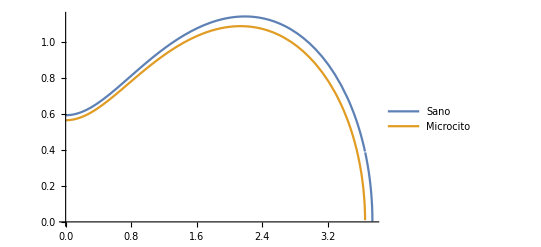

```mathematica
Plot[{cassini[x,2.6,2.7,0.8128],cassini[x,2.6*0.9761,2.7*0.9761,0.8128*0.9761]},{x,0,3.75},PlotLegends->{"Sano","Microcito"}]
```

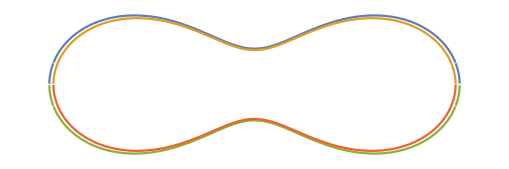

```mathematica
micro=Plot[{cassini[x,2.6,2.7,0.8128],cassini[x,2.6*0.98,2.7*0.98,0.8128*0.98],-cassini[x,2.6,2.7,0.8128],-cassini[x,2.6*0.98,2.7*0.98,0.8128*0.98]},{x,-3.8,3.8},AspectRatio->1/3,Axes->False]
```

```mathematica
cassini[3.67,2.6*0.98,2.7*0.98,0.8128*0.98]*2
```

0.148194

```mathematica
Export["microcito_cass.svg",micro]
```

microcito_cass.svg

```mathematica
Table[{x,cassini[x,2.6*0.98,2.7*0.98,0.8128*0.98]},{x,0,3.67,0.05}]
```

{{0.,0.568295},{0.05,0.569485},{0.1,0.573032},{0.15,0.578862},{0.2,0.586857},{0.25,0.596866},{0.3,0.608709},{0.35,0.622186},{0.4,0.637092},{0.45,0.653215},{0.5,0.670351},{0.55,0.688303},{0.6,0.706884},{0.65,0.725924},{0.7,0.745264},{0.75,0.764763},{0.8,0.78429},{0.85,0.803732},{0.9,0.822985},{0.95,0.84196},{1.,0.860576},{1.05,0.878762},{1.1,0.896456},{1.15,0.913603},{1.2,0.930155},{1.25,0.946071},{1.3,0.961311},{1.35,0.975844},{1.4,0.98964},{1.45,1.00267},{1.5,1.01492},{1.55,1.02636},{1.6,1.03697},{1.65,1.04673},{1.7,1.05564},{1.75,1.06366},{1.8,1.07079},{1.85,1.07701},{1.9,1.08231},{1.95,1.08667},{2.,1.09007},{2.05,1.09249},{2.1,1.09393},{2.15,1.09436},{2.2,1.09375},{2.25,1.0921},{2.3,1.08937},{2.35,1.08553},{2.4,1.08057},{2.45,1.07444},{2.5,1.06712},{2.55,1.05855},{2.6,1.04871},{2.65,1.03753},{2.7,1.02497},{2.75,1.01095},{2.8,0.995402},{2.85,0.978247},{2.9,0.959385},{2.95,0.938702},{3.,0.916064},{3.05,0.891312},{3.1,0.864255},{3.15,0.834659},{3.2,0.802233},{3.25,0.766609},{3.3,0.727306},{3.35,0.683683},{3.4,0.634838},{3.45,0.579442},{3.5,0.515376},{3.55,0.438846},{3.6,0.341562},{3.65,0.194517}}

#### Cálculo de volumen, área

```mathematica
vol = 4 Pi * NIntegrate[
   x * 0.8128 * Sqrt[-2.6^2 - x^2 + Sqrt[4 * x^2 * 2.6^2 + 2.7^4]], 
   {x, 0, 3.7483}]
   
area = 4 Pi NIntegrate[r*Sqrt[1+(cassini[r,2.6,2.7,0.8128])^2],{r,0,3.7483}]
```

80.6307

120.761

```mathematica
vol*0.9761
```

68.0235

```mathematica
vol = 4 Pi * NIntegrate[
   x * (0.8128*0.98) * Sqrt[-(2.6*0.98)^2 - x^2 + Sqrt[4 * x^2 * (2.6*0.98)^2 + (2.7*0.98)^4]], 
   {x, 0, 3.67}]
```

74.3635

```mathematica
4/3*Pi*(2.68)^3
```

80.6293

```mathematica
cassini[0,2.6,2.7,0.8128]
```

0.591727

### Cassini similar a eritrocito real reportado por Tsinopoulos et al

```mathematica
Clear[a]
```

```mathematica
(*Ecuación Tsang*)
zT[x_,R_]:=((1-(x/R)^2)^(0.5))*(0.72+4.152*(x/R)^2-3.426*(x/R)^4)

(*Cassini reescrita considerando el radio máximo de R=3.825 um y c=1 um*)
(*Aquí se toma a b^2=R^2-a^2*)

cassiniTsi[x_,a_,R_]:=(-a^2-x^2+(4 x^2 a^2+(R^2-a^2)^2)^(1/2))^(1/2)

(*Ajuste de Cassini a Tsang*)

data=Table[zT[x,3.825],{x,-3.825,3.825}];

(*Si se pone como condición que en z(0) el grosor sea de 0.71 de forma que el grosor mínimo total sea de 1.42 como lo reportado*)
a[R_,z0_]:=Sqrt[(R^2-z0^2)/2]
a[3.825,0.71]
```

2.65768

```mathematica
Sqrt[3.825^2-2.65768^2]
```

2.75088

```mathematica
datazT=Table[{x,zT[x,3.825]},{x,-3.825,3.825}];
dataCass=Table[{x,cassiniTsi[x,a[3.825,0.71],3.825]},{x,-3.825,3.825}];
MaximalBy[datazT,Last]
MaximalBy[dataCass,Last]
zT[0,3.825]
cassiniTsi[0,a[3.825,0.71],3.825]
```

{{2.175,1.40196}}

{{2.175,1.42249}}

0.72

0.71

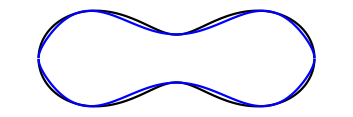

```mathematica
comparacionGeometrias=Plot[{Style[cassiniTsi[x,a[3.825,0.71],3.825],Black],Style[-cassiniTsi[x,a[3.825,0.71],3.825],Black],
                            Style[zT[x,3.825],Blue],Style[-zT[x,3.825],Blue]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

#### Cálculo de volumen, área

```mathematica
vol = 4 Pi * NIntegrate[
   x * cassiniTsi[x,a[3.825,0.71],3.825], 
   {x, 0, 3.825}]
   
area = 4 Pi NIntegrate[r*Sqrt[1+(cassiniTsi[r,a[3.825,0.71],3.825])^2],{r,0,3.825}]
```

104.788

140.882

### Comparación geometrías (original vs Real)

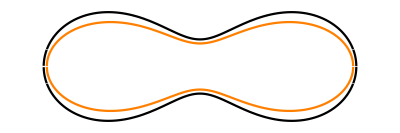

```mathematica
comparacionGeometrias=Plot[{Style[cassiniTsi[x,a[3.825,0.71],3.825],Black],Style[-cassiniTsi[x,a[3.825,0.71],3.825],Black],
                            Style[cassini[x,2.6,2.7,0.83],Orange],Style[-cassini[x,2.6,2.7,0.83],Orange]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

## Cálculos